## Naive way to calculate the area

```mathematica
InterAreaInt[x1_, x2_, y1_, y2_, r1_, r2_] :=Integrate[Boole[(x - x1)^2 + (y - y1)^2<r1^2&&(x - x2)^2 + (y - y2)^2<r2^2],{x,Min[x1 - r1, x2 - r2],Max[x1 + r1, x2+ r2]},{y,Min[y1 - r1, y2 - r2],Max[y1 + r1, y2+ r2]}]
```

```mathematica
Manipulate[InterAreaInt[x1, x2, y1, y2, r1, r2], {x1, -5, 5}, {x2, -5, 5}, {y1, -5, 5}, {y2, -5, 5}, {r1, 0, 3}, {r2, 0, 3}]
```

## Preparations for intersection area

```mathematica
R1 = 1;
R2 = 0.5;
```

```mathematica
F1= 2 * ArcCos[(R1^2- R2^2 + d^2)/(2R1 d)];
F2= 2 * ArcCos[(R2^2- R1^2 + d^2)/(2R2 d)];
S1= R1^2 * (F1 - Sin@F1)/2;
S2= R2^2 * (F2 - Sin@F2)/2;
```

```mathematica
Scom = S1 + S2;
```

```mathematica
fun[d_] := 1/2 R1^2 (2 ArcCos[(d^2+R1^2-R2^2)/(2 d R1)]-Sin[2 ArcCos[(d^2+R1^2-R2^2)/(2 d R1)]])+1/2 R2^2 (2 ArcCos[(d^2-R1^2+R2^2)/(2 d R2)]-Sin[2 ArcCos[(d^2-R1^2+R2^2)/(2 d R2)]])
```

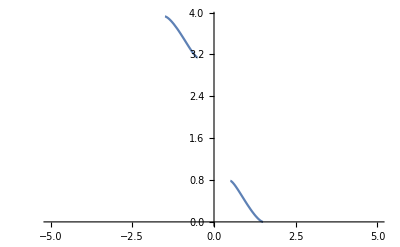

```mathematica
Plot[fun[d], {d, -5 ,5}]
```

## Intersection area of two circles

```mathematica
InterArea[r1_, r2_, d_] := Piecewise[
{{1/2 r1^2 (2 ArcCos[(d^2+r1^2-r2^2)/(2 Abs@d r1)]-Sin[2 ArcCos[(d^2+r1^2-r2^2)/(2 Abs@d r1)]])+1/2 r2^2 (2 ArcCos[(d^2-r1^2+r2^2)/(2Abs@d r2)]-Sin[2 ArcCos[(d^2-r1^2+r2^2)/(2 Abs@d r2)]]), Abs@d ≤ (r1 + r2) &&Min[r1, r2] ≥ Max[r1, r2] - Abs@d}, {Min[r1, r2]^2 * π,Min[r1, r2] ≤ Max[r1, r2] - Abs@d}}] (*Зависимость площади перекрытия двух кругов от их радиусов и расстояния между ними*)
```

## Movement at a distance

```mathematica
Manipulate[Plot[InterArea[r1, r2, √(r^2 + b^2)], {r, -5, 5}, PlotRange->{{-5, 5}, {0, 5}}], {b,0, 5}, {r1, 0, 5}, {r2, 0, 5}]
```

```mathematica
|
```

## Area of intersection of row of circles

```mathematica
(*r1 - pipe circle, r2 - row of identical circles, d - distance between the centers of row circles; x, y - the coordinates of the pipe circle (the begging of the row coordinates are (0,0), the coordinates of the n-th row circle are (n*d, 0))*)
InterRowArea[r1_, r2_, d_, x_, y_] := Module[{dist, cordNormed},
cordNormed=√(Mod[x, d]^2 + y^2);
dist = If[cordNormed < d/2, cordNormed, d - cordNormed];
 InterArea[r1, r2, dist]
]
```

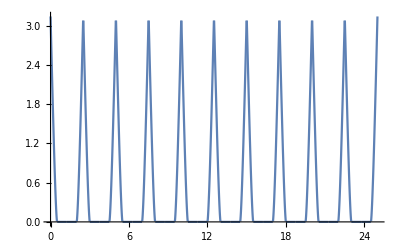

```mathematica
Plot[InterRowArea[1, 1, 10, 4x, 0], {x, 0, 25}]
```

```mathematica
out = Play[InterRowArea[1, 3, 10,  6000* t, 0], {t, 0, 2}]
```

-Graphics-

```mathematica
Export["~/Music/inter_sound.wav", out]
```

Audio`AudioRasterize::interr: An internal error occurred: Audio`AudioRasterize.

General::stop: Further output of Audio`AudioRasterize::interr will be suppressed during this calculation.

Export::nodta: … contains no data that can be exported to the WAV format.

$Failed

```mathematica
FourierSeries[InterRowArea[1, 3, 10,  100 t, 0], t, 3] (*doesn't work(( *)
```

$Aborted

```mathematica
data = Table[InterRowArea[5, 1, 10, 6000x, 0] , {x, 0, 0.05, 0.000001}];
```

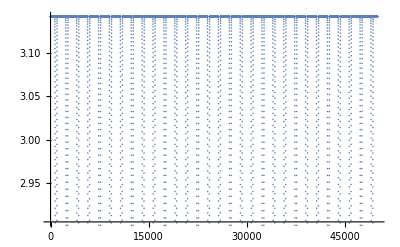

```mathematica
ListPlot[data]
```

```mathematica
ft =Fourier[data, FourierParameters->{-1, 1}];
```

```mathematica
sr=Length[ft] / 0.05;
```

```mathematica
ff=Table[(n-1)*sr/Length[ft],{n,Length[ft]}]//N;
```

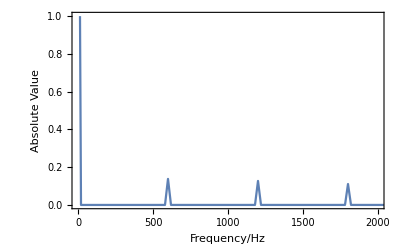

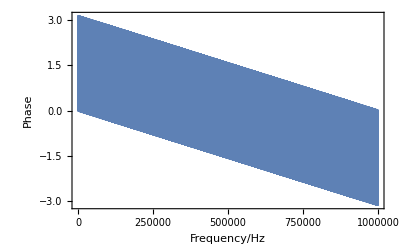

```mathematica
ListLinePlot[Transpose[{ff,Abs[ft]}],PlotRange->{{0, 2000}, {0, 1}},Frame->True,FrameLabel->{"Frequency/Hz","Absolute Value"}]
ListLinePlot[Transpose[{ff,Arg[ft]}],PlotRange->All,Frame->True,FrameLabel->{"Frequency/Hz","Phase"}]
```